# WCG analysis diff 1946-1960

## Directory

```mathematica
datadir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/

## Program

```mathematica
largestPosition[l_List]:=Module[{largest},
largest=Max[l];
Position[l,largest]
]
```

```mathematica
selectEdgeAs["DST"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association];*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]
]
```

```mathematica
selectGraphAs["DST"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association];*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]//Graph
]
```

```mathematica
selectGraphAs["SRC"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[1]]&];
gkeys=Map[#[[1,1]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association]*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]//Graph
]
```

```mathematica
selectEdgeAs["SRC"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[1]]&];
gkeys=Map[#[[1,1]]&,gth];
(*as=Inner[Rule,gkeys,gth,Association]*);
as=Association[MapThread[Rule,{gkeys,gth}]];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]
]
```

## Basic information

上位1%被引用論文 {citingPMID(代表) -> citedPMID, count}

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top1perc-cited-artByyear.save"];
```

```mathematica
Do[citedPMIDTop1perc[n]=Map[#[[1,2]]&,citedArtlistTop1perc[n]],
{n,1950,2020,5}]
```

## Previous : WCG 1946 - 1955

### Data

```mathematica
previousG=1955
```

1955

Graph

```mathematica
file[previousG]=datadir<>"WCG_1946-"<>ToString[previousG]<>".wl"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/WCG_1946-1955.wl

前世代WCG数*

```mathematica
(WCGlist[previousG]=Get[file[previousG]])//Length
```

3851

WCGをVertexListにする：

```mathematica
(WCGlistV[previousG]=Map[VertexList,WCGlist[previousG]])//Length
```

3851

Vertex名(PMID)からそのVertexがどのWCGに含まれるかそのpositionを返す。

```mathematica
PMIDtoWCGPos[previousG]=Association[Flatten[MapIndexed[Apply[Outer,{Rule,#1,#2}]&,WCGlistV[previousG]]]];
```

```mathematica
largestWCGPos[previousG]=Flatten[largestPosition[Map[VertexCount,WCGlist[previousG]]]]
```

{1}

```mathematica
WCGlargest[previousG]=WCGlist[previousG][[1]];
```

Nodes

```mathematica
(WCGNodes[previousG]=Map[VertexList,WCGlist[previousG]])//Length
```

3851

Edges

```mathematica
(WCGEdges[previousG]=Map[EdgeList,WCGlist[previousG]])//Length
```

3851

Global Graph

```mathematica
GlobalGraph[previousG]=Graph[Flatten[WCGEdges[previousG]]];
```

```mathematica
(*GlobalEdge[previousG]=EdgeList[GlobalGraph[previousG]];*)
```

## Current : WCG 1946 - 1960

### Data

```mathematica
currentG=1960
```

1960

Graph

```mathematica
file[currentG]=datadir<>"WCG_1946-"<>ToString[currentG]<>".wl"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/WCG_1946-1960.wl

```mathematica
(WCGlist[currentG]=Get[file[currentG]])//Length
```

4624

```mathematica
largestWCGPos[currentG]=Flatten[largestPosition[Map[VertexCount,WCGlist[currentG]]]]
```

{1}

```mathematica
WCGlargest[currentG]=WCGlist[currentG][[1]];
```

Nodes

```mathematica
(WCGNodes[currentG]=Map[VertexList,WCGlist[currentG]])//Length
```

4624

Edges

```mathematica
(WCGEdges[currentG]=Map[EdgeList,WCGlist[currentG]])//Length
```

4624

Global Graph

```mathematica
GlobalGraph[currentG]=Graph[Flatten[WCGEdges[currentG]]];
```

## Diff : 1946-1955 < 1946-1960

A. 新規に発生した引用関係*

```mathematica
(WCGtotaledgeDiff[previousG,currentG]=Complement[Flatten[Map[EdgeList,WCGlist[currentG]]],Flatten[Map[EdgeList,WCGlist[previousG]]]])//Length
```

291655

B. 新規に発生した引用関係からSrc/Dstを混ぜてVertexListをつくる

```mathematica
(WCGtotalnodeDiffU[previousG,currentG]=Union[Flatten[Apply[List,WCGtotaledgeDiff[previousG,currentG],Infinity]]])//Length
```

166589

B-1. 上記VertexListより前年代のVertexでもあるものを選択（グラフを拡張するキーとなる存在:コネクション論文）

```mathematica
(WCGtotalnodeIS[previousG,currentG]=Intersection[Flatten[WCGNodes[previousG]],WCGtotalnodeDiffU[previousG,currentG]])//Length
```

42790

B-2. 上記Vertexに含まれるtop1%論文（コネクション論文かつtop1%論文）-> citedPMIDTop1percCon

```mathematica
citedPMIDTop1percCon[previousG]=Intersection[citedPMIDTop1perc[previousG],WCGtotalnodeIS[previousG,currentG]]
```

{14772207,14822727,14907713,15395398,15398090,15398551,16561366,16694480,16694558,16695228,16695286,16695568,16745305,16746620,16747230,16747456,16747508,16747652,16747674,16747784,16747907,16747948,16748220,16748273,16748381,16991878,17247100,17247150,17760012,18128147}

B-3. 新規に発生した引用のうち主要論文に対する引用*

:まずAssociationを作成:

```mathematica
WCGtotaledgeDiffGatherDSTAs=Association[Map[#[[1,2]]->#&,GatherBy[WCGtotaledgeDiff[previousG,currentG],#[[2]]&]]];
```

:AssociationをMap:

```mathematica
(fconEdgediff[currentG]=Map[WCGtotaledgeDiffGatherDSTAs,citedPMIDTop1percCon[previousG]]//Flatten)//Length
```

1235

## WCG connection of all of previous part

A-1. 新規に発生した引用関係により結合が発生した前世代WCG {WCG ID, count} (すべてが結合されたわけではない)*

```mathematica
newConnectedWCGcount[currentG]=(previousWCGfconPartAll[currentG]=Cases[Map[PMIDtoWCGPos[previousG],WCGtotalnodeIS[previousG,currentG]],_Integer]//Tally)//Length
```

1485

## WCG elongation matrix : 1946-1955 < 1946-1960

Current WCGのPMIDより、{previous-WCG-ID : current-WCG-ID}のペアを作成する。
Current WCGのPMID（デスティネーション）を渡すと前世代WCGのID（位置）を返す関数を作成する。

```mathematica
aspv=Association[Flatten[Table[Map[#->n&,VertexList[WCGlist[previousG][[n]]]],{n,Length[WCGlist[previousG]]}]]];
```

```mathematica
(cedList=Map[Map[#[[2]]&,EdgeList[#]]&,WCGlist[currentG]])//Length
```

4624

```mathematica
Timing[(elMat[currentG]=DeleteCases[Map[Map[aspv[#]&,#]&,cedList],_Missing,{2}])//Length]
```

{0.318796,4624}

```mathematica
Save[datadir<>"elongationMat.save",elMat]
```

## WCG elongation connection : 1946-1955 < 1946-1960

A-2. 新規に発生した引用関係に対して前世代の引用先がどのWCGに属するか(Missingあり <- 落としている) {“PMID” -> WCG ID}

```mathematica
(WCGtotaledgeDiffEff[previousG,currentG,"previous WCG ID"]=Cases[  Map[#[[1]]->PMIDtoWCGPos[previousG][#[[2]]]&,WCGtotaledgeDiff[previousG,currentG]]  ,x_/;Head[x[[2]]]==Integer])//Length
```

114118

ギャザー.ユニーク化

```mathematica
(WCGconUnion[previousG,currentG,"previous WCG ID"]=Map[Union,  GatherBy[WCGtotaledgeDiffEff[previousG,currentG,"previous WCG ID"],#[[1]]&]  ])//Length
```

24943

A-3. 新規に発生した引用関係により異なる前世代WCGを結合する論文（ユニーク化）*

```mathematica
newMetaconnectedcount[currentG]=(WCGelongationconUnion[previousG,currentG,"previous WCG ID"]=Cases[WCGconUnion[previousG,currentG,"previous WCG ID"],x_/;Length[x]>1])//Length
```

1942

A-4. 新規に結合された前世代WCG（全てが統合された訳ではない）*

```mathematica
newMetaconnectedWCGcount[currentG]=(WCGnewconnected[previousG,currentG]=Union[Map[#[[2]]&,Flatten[WCGelongationconUnion[previousG,currentG,"previous WCG ID"]]]])//Length
```

1185

## Visualization (top 1% article part)

### グラフの主要接続部分のパターン定義

主要接続部分とはグラフ差分のうちで主要論文が関与する部分。本研究の流れではフォワードコネクション （主要論文の被引用） を使うのが妥当か。

コネクション論文かつ上位1%論文付近のネットワーク（当年代）

:フォワードコネクション（上位1%コネクション論文が引用される;年代を進める）previous

```mathematica
citedPMIDTop1percCon[previousG]
```

{14772207,14822727,14907713,15395398,15398090,15398551,16561366,16694480,16694558,16695228,16695286,16695568,16745305,16746620,16747230,16747456,16747508,16747652,16747674,16747784,16747907,16747948,16748220,16748273,16748381,16991878,17247100,17247150,17760012,18128147}

### 1960におけるグラフの接続部分

#### *フォワード

関数のSubgraph[]と同じ結果が欲しければ、結果のvertexlistをキーにしてSubgraph[]する。（今回不要なはず）

```mathematica
fconGraph[currentG]=selectGraphAs["DST"][GlobalGraph[currentG],citedPMIDTop1percCon[previousG]];
```

```mathematica
vl=VertexList[fconGraph[currentG]];
```

```mathematica
(fconEdgelist[currentG]=EdgeList[fconGraph[currentG]])//Length
```

3043

```mathematica
(fconNodelist[currentG]=VertexList[fconGraph[currentG]])//Length
```

2567

#### *バックワード

```mathematica
(fconEdgeSRC[currentG]=Union[Map[#[[1]]&,fconEdgelist[currentG]]])//Length
```

2540

```mathematica
AbsoluteTiming[bconGraph[currentG]=selectGraphAs["SRC"][GlobalGraph[currentG],fconEdgeSRC[currentG]]]
```

{0.725412,}

```mathematica
(bconNodelist[currentG]=VertexList[bconGraph[currentG]])//Length
```

17423

top1%論文による前世代グラフのWCG接続

```mathematica
previousWCGfconPartTop1perc[currentG]=Cases[Map[PMIDtoWCGPos[previousG],bconNodelist[currentG]],_Integer]//Tally//Sort
```

{{1,10564},{55,1},{81,1},{135,1},{168,1},{189,1},{212,3},{312,1},{489,1},{576,1},{646,1},{704,1},{751,1},{921,1},{1089,1},{1128,1},{1322,1},{1328,1},{1390,2},{1547,1},{1611,1},{1818,1},{1981,1},{2022,1},{2052,1},{2375,1},{2398,1},{3219,1},{3293,1},{3363,1},{3591,1},{3710,1},{3731,2},{3796,1}}

```mathematica
(*Export["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/connectionpartGraph_"<>ToString[previousG]<>"-"<>ToString[currentG]<>".wl",bconGraph[currentG]]*)
```

### 1955と1960のグラフの差分

#### *フォワード : 差分

```mathematica
vstyle=Map[#->Orange&,citedPMIDTop1percCon[previousG]]
```

{14772207→RGBColor[1, 0.5, 0],14822727→RGBColor[1, 0.5, 0],14907713→RGBColor[1, 0.5, 0],15395398→RGBColor[1, 0.5, 0],15398090→RGBColor[1, 0.5, 0],15398551→RGBColor[1, 0.5, 0],16561366→RGBColor[1, 0.5, 0],16694480→RGBColor[1, 0.5, 0],16694558→RGBColor[1, 0.5, 0],16695228→RGBColor[1, 0.5, 0],16695286→RGBColor[1, 0.5, 0],16695568→RGBColor[1, 0.5, 0],16745305→RGBColor[1, 0.5, 0],16746620→RGBColor[1, 0.5, 0],16747230→RGBColor[1, 0.5, 0],16747456→RGBColor[1, 0.5, 0],16747508→RGBColor[1, 0.5, 0],16747652→RGBColor[1, 0.5, 0],16747674→RGBColor[1, 0.5, 0],16747784→RGBColor[1, 0.5, 0],16747907→RGBColor[1, 0.5, 0],16747948→RGBColor[1, 0.5, 0],16748220→RGBColor[1, 0.5, 0],16748273→RGBColor[1, 0.5, 0],16748381→RGBColor[1, 0.5, 0],16991878→RGBColor[1, 0.5, 0],17247100→RGBColor[1, 0.5, 0],17247150→RGBColor[1, 0.5, 0],17760012→RGBColor[1, 0.5, 0],18128147→RGBColor[1, 0.5, 0]}

```mathematica
vsize=Map[#->7&,citedPMIDTop1percCon[previousG]]
```

{14772207→7,14822727→7,14907713→7,15395398→7,15398090→7,15398551→7,16561366→7,16694480→7,16694558→7,16695228→7,16695286→7,16695568→7,16745305→7,16746620→7,16747230→7,16747456→7,16747508→7,16747652→7,16747674→7,16747784→7,16747907→7,16747948→7,16748220→7,16748273→7,16748381→7,16991878→7,17247100→7,17247150→7,17760012→7,18128147→7}

新しく増えた引用関係（currentのconエッジ - previousのconエッジ）のハイライト

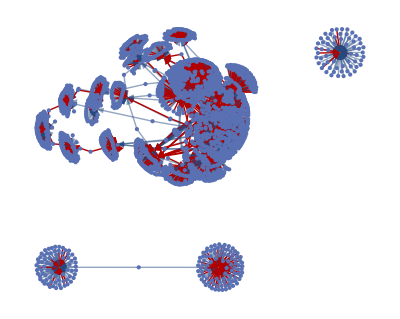

```mathematica
fconGraphD[currentG]=Graph[fconGraph[currentG],GraphHighlight->Flatten[{fconEdgediff[currentG]}],VertexStyle->vstyle,VertexSize->vsize]
```

可視化対象の構造だけはExportしておく。

```mathematica
(*Export[datadir<>"gdiffF_"<>ToString[currentG]<>".wl",fconGraphD[currentG]]*)
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/gdiffF_1960.wl